# The Central Limit Theorem

The Central Limit Theorem is an important result in statistics that states that subject to certain conditions, averages of multiple random variables tend to follow a normal distribution.

May 13, 2017—Stephen Wolfram

## Discovering the Central Limit Theorem

Let’s “discover” the Central Limit Theorem empirically, by looking at collections of random numbers.

Make a list of 10 random real numbers between -1 and 1:

```mathematica
RandomReal[{-1,1},10]
```

{-0.0771015,-0.366985,-0.339309,0.828772,-0.0314546,0.258496,-0.626615,0.903993,0.337799,-0.719367}

These random numbers are uniformly distributed, so if we make a histogram of them, it’ll be flat.

Make a histogram of 1000 random numbers between -1 and 1:

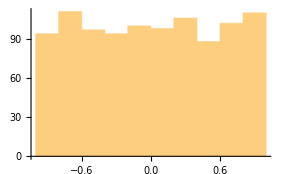

```mathematica
Histogram[RandomReal[{-1,1},1000]]
```

With 100,000 numbers the histogram is almost exactly flat:

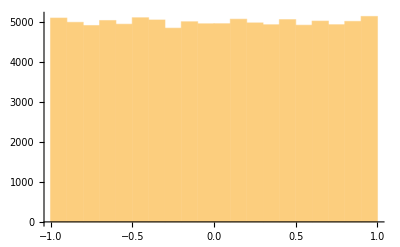

```mathematica
Histogram[RandomReal[{-1,1},100000]]
```

Now let’s start finding means of collections of numbers.

This finds the mean of 10 random real numbers:

```mathematica
Mean[RandomReal[{-1,1},10]]
```

-0.112097

Here is a list of 10 such means:

```mathematica
Table[Mean[RandomReal[{-1,1},10]],10]
```

{-0.112467,0.0172069,0.0826008,0.134617,-0.220979,-0.0600067,-0.14143,0.171051,-0.13263,0.0301039}

Here is the distribution of 1000 such means:

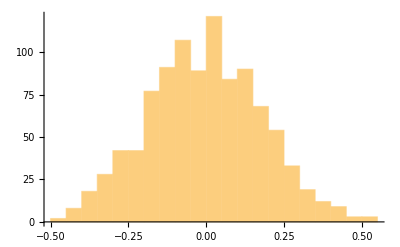

```mathematica
Histogram[Table[Mean[RandomReal[{-1,1},10]],1000]]
```

Here is the distribution for 100,000 means:

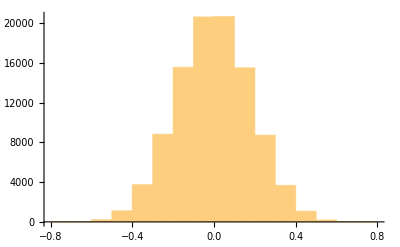

```mathematica
Histogram[Table[Mean[RandomReal[{-1,1},10]],100000]]
```

The distribution for the means is not flat; instead it’s a bell-shaped curve.

It’s easier to see the shape of the curve if we use smaller bins; here width 0.01:

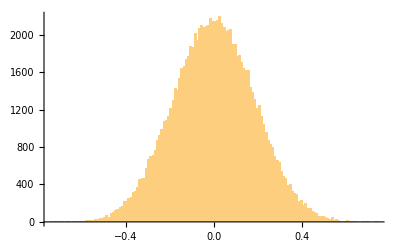

```mathematica
Histogram[Table[Mean[RandomReal[{-1,1},10]],100000],{.01}]
```

If we only put 5 numbers into the mean, we still get a very similar result:

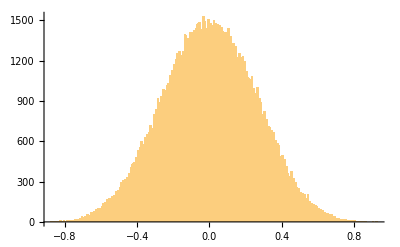

```mathematica
Histogram[Table[Mean[RandomReal[{-1,1},5]],100000],{.01}]
```

The crucial thing about the Central Limit Theorem is that it holds for a wide range of different underlying random distributions.

If we cube each random number, the distribution of the results isn’t flat:

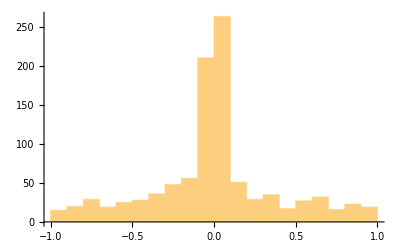

```mathematica
Histogram[Table[RandomReal[{-1,1}]^3,1000]]
```

The distribution of the means is still the same shape:

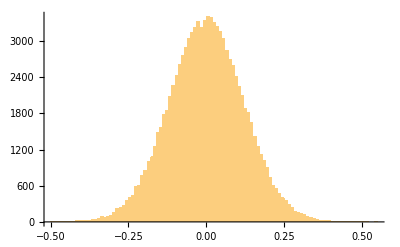

```mathematica
Histogram[Table[Mean[Table[RandomReal[{-1,1}]^3,10]],100000],{.01}]
```

If we square each number, we’ll always get results that are positive:

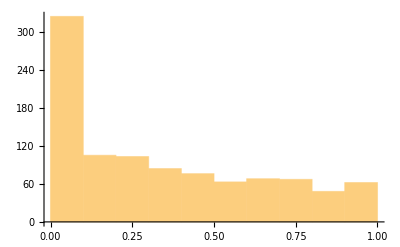

```mathematica
Histogram[Table[RandomReal[{-1,1}]^2,1000]]
```

The distribution of the means is still the same shape, though its center (mean) is shifted:

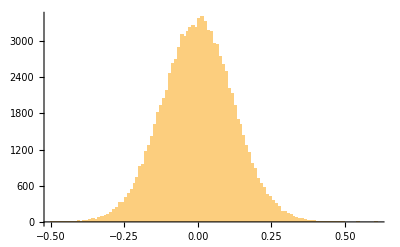

```mathematica
Histogram[Table[Mean[Table[RandomReal[{-1,1}]^3,10]],100000],{.01}]
```

## The Normal Distribution

Plot a normal distribution with mean 0 and variance 1:

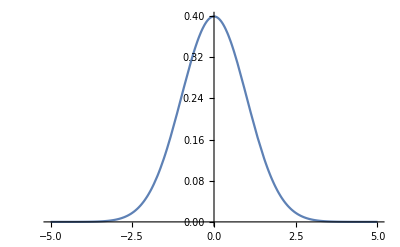

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5}]
```

Here is the functional form:

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

Let’s compare the results from data with an actual normal distribution.

Here is data from 100,000 cubes of uniform random numbers:

```mathematica
data=Table[Mean[Table[RandomReal[{-1,1}]^3,10]],100000];
```

The mean of this data is very close to 0:

```mathematica
Mean[data]
```

0.000596174

This is the standard deviation of the data:

```mathematica
StandardDeviation[data]
```

0.119462

Make a plot of a normal distribution with this mean and standard deviation:

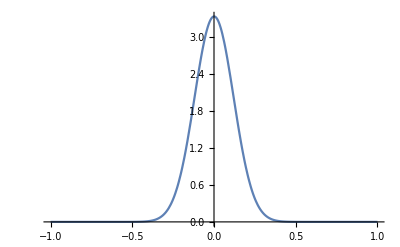

```mathematica
plot=Plot[PDF[NormalDistribution[Mean[data],StandardDeviation[data]],x],{x,-1,1}]
```

To compare with histograms, we want the histogram (like the distribution) to be normalized to have total area 1.

Normalize the histogram so its total area is 1:

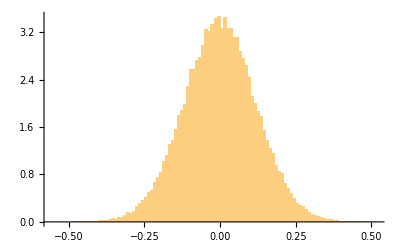

```mathematica
hist=Histogram[Table[Mean[Table[RandomReal[{-1,1}]^3,10]],100000],{.01},"PDF"]
```

Show the histogram and plot together; they agree!

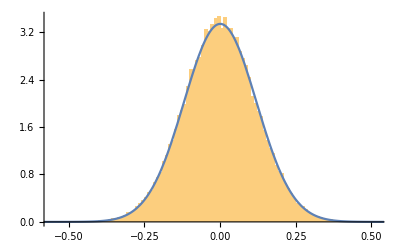

```mathematica
Show[hist,plot]
```

## Towards the Normal Distribution

If we don’t average multiple numbers at all, we’ll just see the underlying distribution of those numbers. Let’s see what happens if we average successively more numbers.

Here’s the result “average 1 number” (i.e not averaging at all):

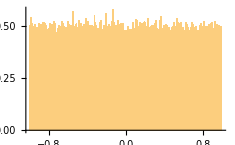

```mathematica
Histogram[Table[Mean[Table[RandomReal[{-1,1}],1]],100000],{.01},"PDF"]
```

Here’s the result averaging 2 numbers:

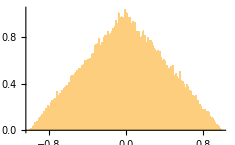

```mathematica
Histogram[Table[Mean[Table[RandomReal[{-1,1}],2]],100000],{.01},"PDF"]
```

Here are the results averaging up to 10 numbers:

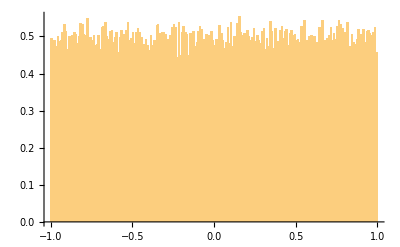
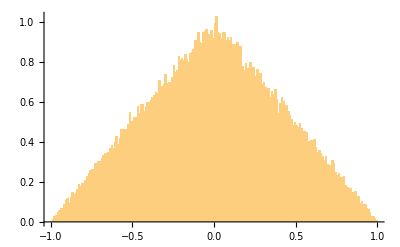
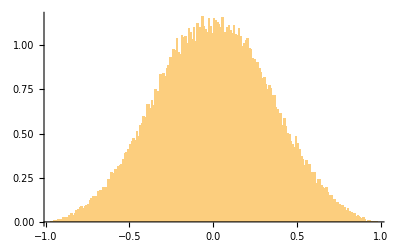
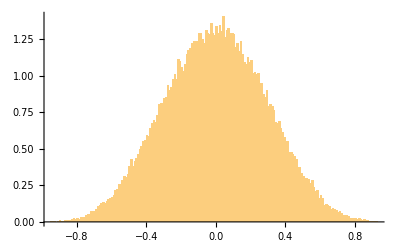
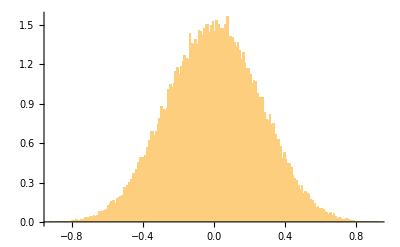
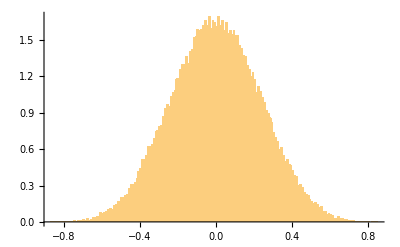
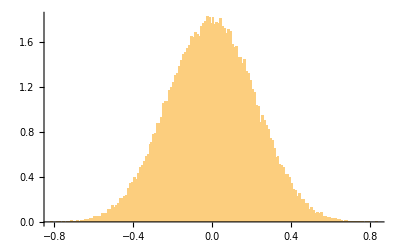
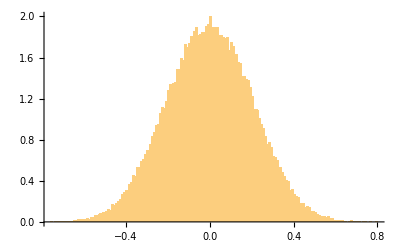

```mathematica
Table[Histogram[Table[Mean[Table[RandomReal[{-1,1}],n]],100000],{.01},"PDF"],{n,10}]
```

Beyond about 5 numbers, the results are indistinguishable: the distribution has converged to the normal distribution, just as the Central Limit Theorem says it should.

Let’s try the same thing, starting from squared numbers. The original distribution looks quite different. Average 2 numbers it still looks different. But with about 5 numbers, it’s already converged to the same normal distribution.

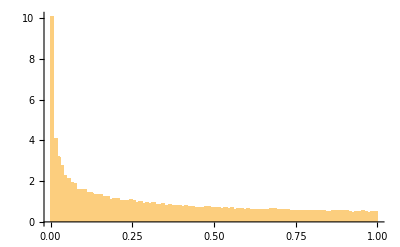
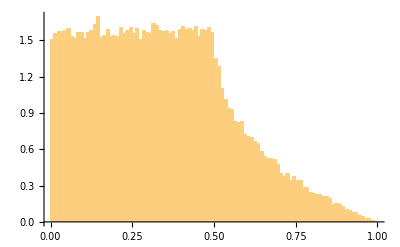
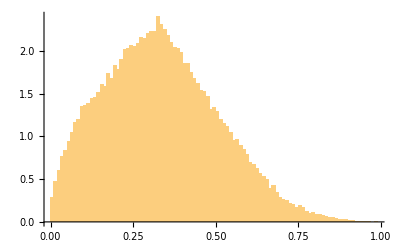
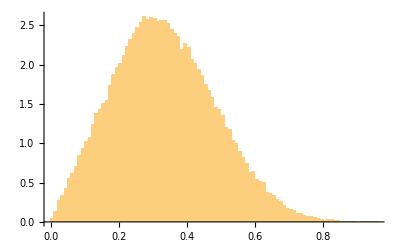
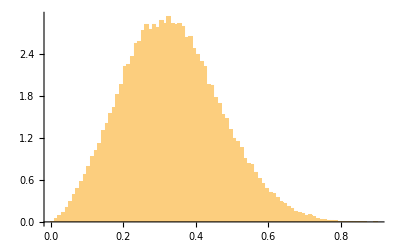
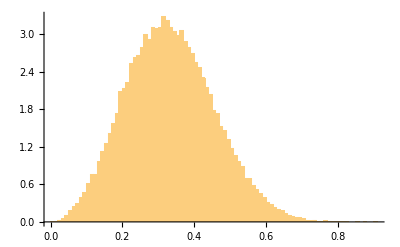
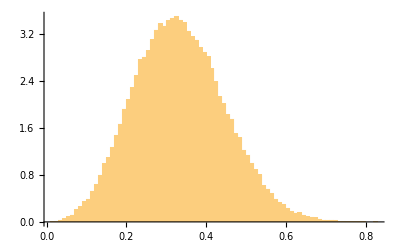
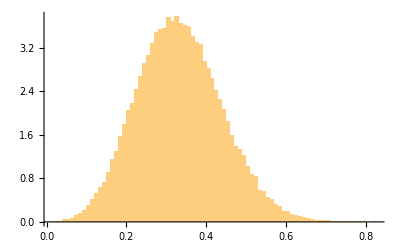

```mathematica
Table[Histogram[Table[Mean[Table[RandomReal[{-1,1}]^2,n]],100000],{.01},"PDF"],{n,10}]
```

## The Normal Distribution in 2D and Beyond

One can define “multinormal” distributions in any number of dimensions. In 2D, the analog of standard deviation is a matrix that includes cross-correlations.

Find the functional form of a 2D normal distribution with mean 0,0 and unit standard deviation:

```mathematica
PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x,y}]
```

(ⅇ^(1/2 (-x^2-y^2)))/(2 π)

Plot the distribution:

```mathematica
Plot3D[PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x,y}],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

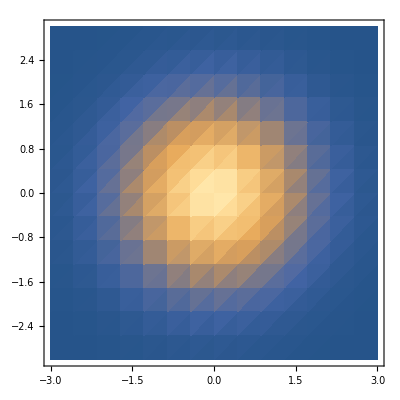

```mathematica
DensityPlot[PDF[MultinormalDistribution[{0,0},{{1,0},{0,1}}],{x,y}],{x,-3,3},{y,-3,3}]
```

Like in 1D, one can find values and then average them.

10,000 points at random coordinates in 2D:

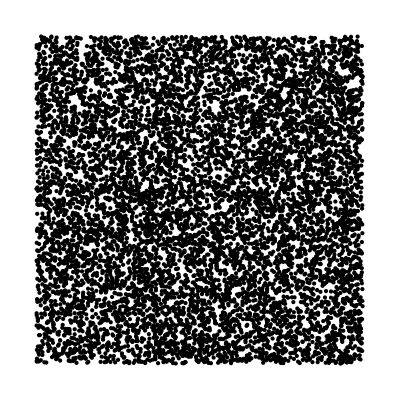

```mathematica
Graphics[Point[Table[RandomReal[{-1,1},2],10000]]]
```

Points obtained by averaging 5 positions together:

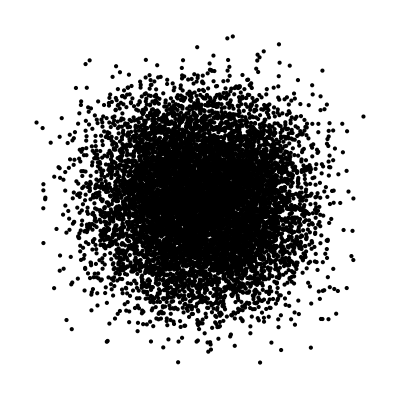

```mathematica
Graphics[Point[Table[Mean[RandomReal[{-1,1},{5,2}]],10000]]]
```

Results with successive larger amounts of averaging:

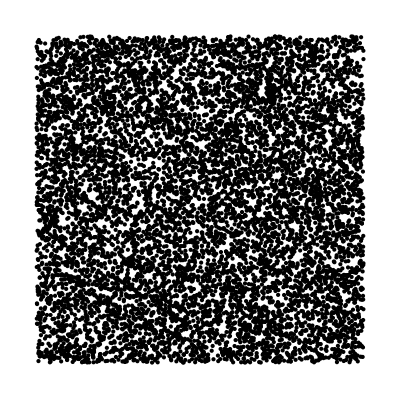
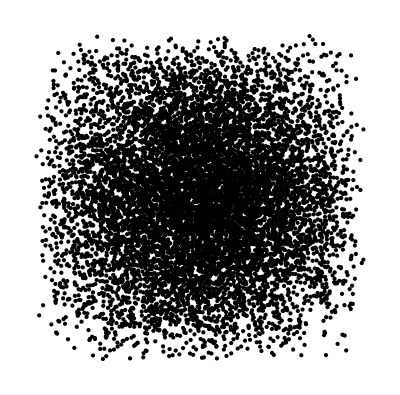
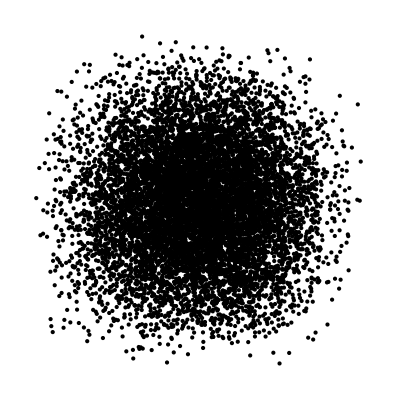
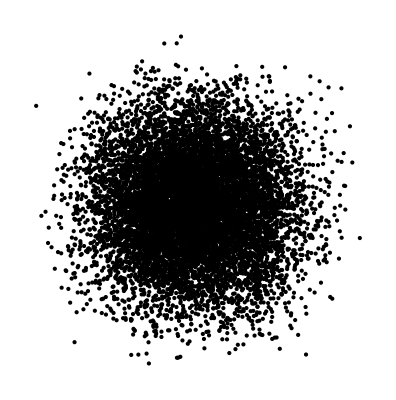
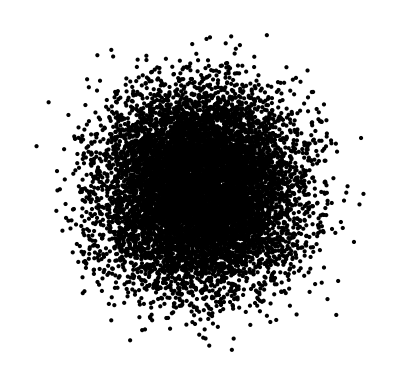
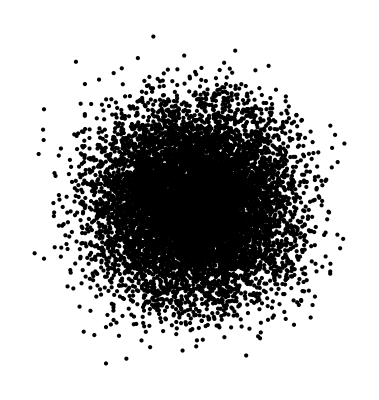
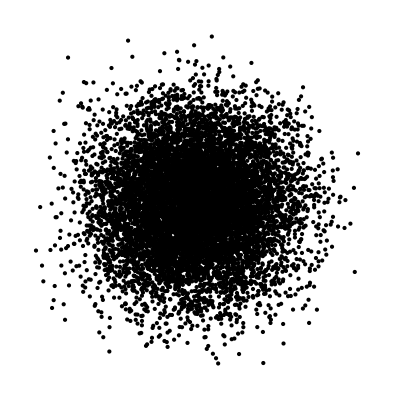
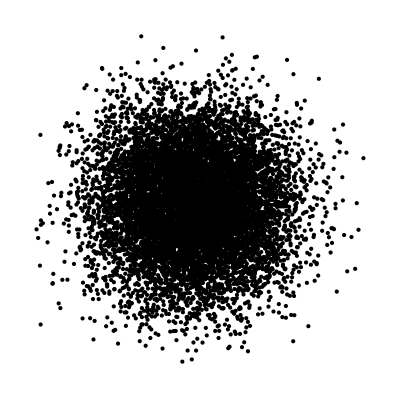

```mathematica
Table[Graphics[Point[Table[Mean[RandomReal[{-1,1},{n,2}]],10000]]],{n,1,10}]
```

One can do just the same in 3D.

Here is a point cloud in 3D, with each point obtained by averaging 5 values together:

```mathematica
Graphics3D[Point[Table[Mean[RandomReal[{-1,1},{5,3}]],10000]]]
```

-Graphics3D-

It’s a little clearer what’s going on if one uses opacity .2 for each point:

```mathematica
Graphics3D[Style[Point[Table[Mean[RandomReal[{-1,1},{5,3}]],10000]],Opacity[.2]]]
```

-Graphics3D-

## Random Walks

One way to end up with a normal distribution is to look at the end points of a collection of random walks. Because of the Central Limit Theorem it doesn’t usually matter what the details of the individual steps are like.

Successively accumulate random numbers uniformly distributed between -1 and 1 to form a random walk:

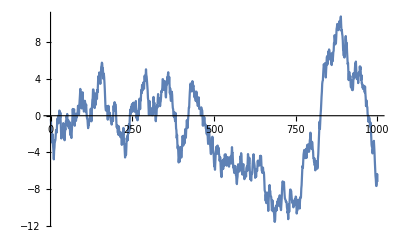

```mathematica
ListLinePlot[Accumulate[RandomReal[{-1,1},1000]]]
```

Make a histogram of the end points of 10000 random walks of length 100:

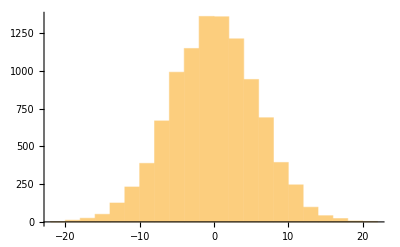

```mathematica
Histogram[Table[Total[RandomReal[{-1,1},100]],10000]]
```

As the number of steps in the random walks increases, the variance steadily gets bigger:

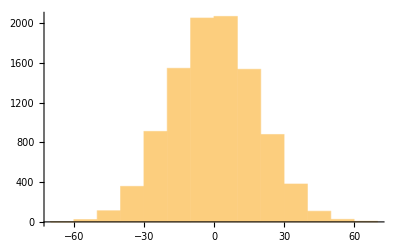

```mathematica
Histogram[Table[Total[RandomReal[{-1,1},1000]],10000]]
```

Make a 2D random walk with 1000 steps of unit length, with a random direction for each step:

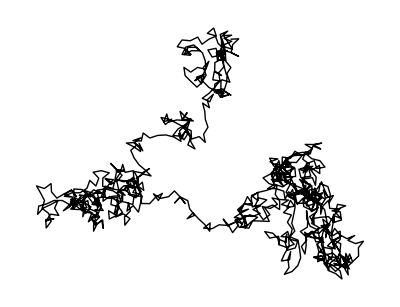

```mathematica
Graphics[Line[AnglePath[RandomReal[{0,2Pi},1000]]]]
```

Make a 3D histogram of where the paths end up:

```mathematica
Histogram3D[Table[Last[AnglePath[RandomReal[{0,2Pi},100]]],10000]]
```

-Graphics3D-

## What Isn’t a Normal Distribution

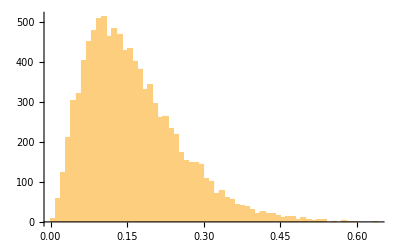

```mathematica
Histogram[Table[GeometricMean[Table[RandomReal[{-1,1}],10]^2],10000],{.01}]
```

Levy flights....

Stock market prices:

```mathematica
DateListPlot[FinancialData["GE",{Now-LinguisticAssistant,Now}]]
```

DateListPlot[Missing[NotAvailable]]

Further Explorations

Investigate the rate of convergence to the normal distribution

Investigate the distributions of the largest digits in powers of 2

Authorship information

Stephen Wolfram

05/13/17

s.wolfram@wolfram.com